# Compound Matrix Method

## Installation

The following command will install the version 0.5 from the website. Check the github page for more recent versions.

```mathematica
Needs["PacletManager`"]
PacletInstall["https://github.com/SPPearce/CompoundMatrixMethod/releases/download/v0.5/CompoundMatrixMethod-0.5.paclet"]
```

Implementation of the Compound Matrix Method to calculate the Evans function, in order to solve boundary value eigenvalue problems.

```mathematica
Needs["CompoundMatrixMethod`"]
```

## Examples

Example 1: Second order equation with constant coefficients

Second order ODE: y''(x) + λ^2 y(x) =0, subject to y(0)=y(L)=0. The roots to this can be found analytically to be nπ/L, n ∈ ℤ. 
Converting to a matrix equation, we let y_1=y,y_2=y', then y_1'=y_2,y_2'=-λ^2 y_1 and hence y' =A y, where A=(0 | 1
-λ^2 | 0).
These boundary conditions can be written as matrices as B=C=(1 | 0
0 | 0). 
We can then evaluate the Evans function at a given value of λ=λ_0, e.g. for λ=1  (with L=2):

```mathematica
CompoundMatrixMethod[{λ,1},{{{0,1},{-λ^2,0}},DiagonalMatrix[{1,0}],DiagonalMatrix[{1,0}],{x,0,2}}]
```

0.909297

This function is analytic, and its zeroes correspond to eigenvalues of the original system:

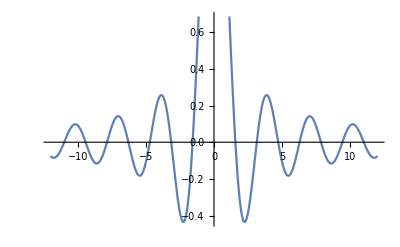

```mathematica
With[{L=2},
Plot[CompoundMatrixMethod[{λ,λ0},{{0,1},{-λ^2,0}},DiagonalMatrix[{1,0}],DiagonalMatrix[{1,0}],{x,0,L}],{λ0,-12,12}]]
```

FindRoot will converge to a root:

```mathematica
With[{L=2},FindRoot[CompoundMatrixMethod[{λ,λ0},{{0,1},{-λ^2,0}},DiagonalMatrix[{1,0}],DiagonalMatrix[{1,0}],{x,0,L}],{λ0,2}]]
```

{λ0→1.5708}

-Graphics-

However, the easier way to feed the system to CompoundMatrixMethod is to use the function ToLinearMatrixForm:

```mathematica
sys=ToLinearMatrixForm[y''[x]+λ^2 y[x]==0,{y[0]==0,y[L]==0},y,{x,0,L}];
```

This returns all the components needed to generate the Evans function at a given λ

```mathematica
CompoundMatrixMethod[{λ,1},sys/.L->2]
```

0.909297

And gives the same plot as before:

```mathematica
Plot[CompoundMatrixMethod[{λ,λ0},sys/.L->2],{λ0,-12,12}]
```

-Graphics-

We could also change the boundary values, e.g. for y(0)+2 y'(0)=0, y'(L)=0.

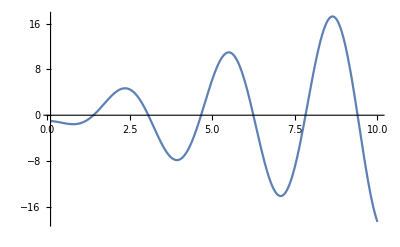

```mathematica
With[{L=2},Plot[CompoundMatrixMethod[{λ,λ0},ToLinearMatrixForm[y''[x]+λ^2 y[x]==0,{y[0]+2y'[0]==0,y'[L]==0},y,{x,0,L}]],{λ0,0.1,10}]]
```

Example 2: Second order equation with complex constant coefficients

This method also works for complex equations , here is y’(x) = ⅈ y(x) + z(x), z'(x)=-λ^2 y(x) + (1-ⅈ)z(x)

```mathematica
example2[λ0_?NumericQ]:=CompoundMatrixMethod[{λ,λ0},{{I,1},{-λ^2,1-I}},DiagonalMatrix[{1,0}],DiagonalMatrix[{1,0}],{x,0,2}]
```

Can find complex roots using FindRoot:

```mathematica
FindRoot[example2[λ0],{λ0,5}]
```

{λ0→4.63338-0.107912 ⅈ}

And can plot the real and imaginary parts in the complex plane, intersections of the two curves show roots.

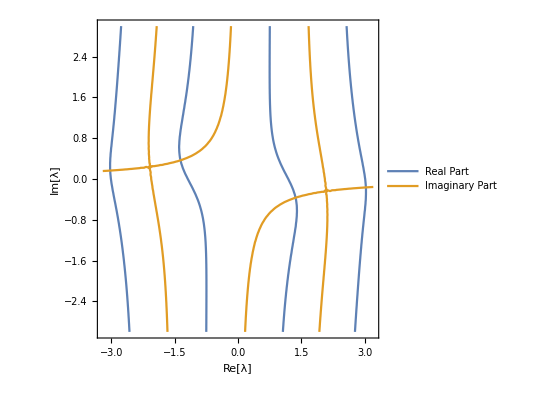

```mathematica
ContourPlot[{Re[example2[λr+I λi]]==0,Im[example2[λr+I λi]]==0},{λr,-3.2,3.2},{λi,-3,3},PlotPoints->30,FrameLabel->{"Re[λ]","Im[λ]"},PlotLegends->{"Real Part","Imaginary Part"}]
```

Example 3: Third order equation with complex eigenvalues

The method also works for odd order equations, for instance y'''- λ^3 y=0, y(0)=y'(0)=0, y(π)=0. 
This equation can be solved using DSolve, and has a range of complex roots

```mathematica
yex3=DSolve[{y'''[x]-λ^3 y[x]==0},y,{x,0,π}][[1]];
cofmat=Table[Coefficient[{y[0]==0,y'[0]==0,y[π]==0}/.yex3/.Equal->Subtract,C[i]],{i,1,3}];
ex3detsol=NSolve[{Simplify[Det[cofmat]]==0,-5≤Re@λ≤5,-5≤Im@λ≤5}]//Chop
```

{{λ→-4.81125},{λ→-3.65655},{λ→-2.50185},{λ→-1.34747},{λ→0},{λ→0},{λ→0},{λ→0.673736-1.16694 ⅈ},{λ→0.673736+1.16694 ⅈ},{λ→1.25092-2.16667 ⅈ},{λ→1.25092+2.16667 ⅈ},{λ→1.82828-3.16667 ⅈ},{λ→1.82828+3.16667 ⅈ},{λ→2.40563-4.16667 ⅈ},{λ→2.40563+4.16667 ⅈ}}

ToLinearMatrixForm gives the 3x3 matrix A, and assigns the boundary conditions correctly.

```mathematica
sys3=ToLinearMatrixForm[{y'''[x]-λ^3 y[x]==0},{y[0]==0,y'[0]==0,y[π]==0},y,{x,0,π}]
```

{{{0,1,0},{0,0,1},{λ^3,0,0}},{{1,0,0},{0,1,0}},{{1,0,0}},{x,0,π}}

```mathematica
FindRoot[CompoundMatrixMethod[{λ,λ0},sys3],{λ0,1+I}]//Chop
```

{λ0→0.673736+1.16694 ⅈ}

Again, we can use ContourPlot to see graphically the solutions (increase PlotPoints to improve accuracy, but takes longer if you do):

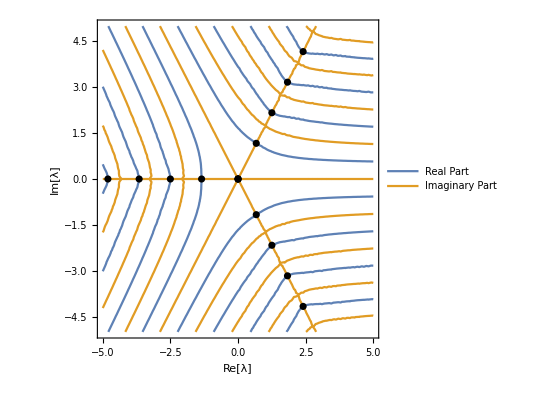

```mathematica
cm3[λ0_?NumericQ]:=CompoundMatrixMethod[{λ,λ0},sys3]
Show[{ContourPlot[{Re[cm3[λr+I λi]]==0,Im[cm3[λr+I λi]]==0},{λr,-5,5},{λi,-5,5},PlotPoints->30,FrameLabel->{"Re[λ]","Im[λ]"},PlotLegends->{"Real Part","Imaginary Part"}],ListPlot[ReIm[λ/.ex3detsol],PlotStyle->Black]}]
```

Example 4: Fourth order equation with non-constant coefficients

ϵ^4 y''''(x)+2 ϵ^2 λd/dx[sin(x)dy/dx]+y==0, subject to y (0)==y''(0)==y'(π/2)==y'''(π/2)==0.

Using the  function to generate the matrix form:

```mathematica
sys=ToLinearMatrixForm[ϵ^4 y''''[x]+2 ϵ^2 λ D[Sin[x]y'[x],x]+y[x]==0,{y[0]==0,y''[0]==0,y'[π/2]==0,y'''[π/2]==0},y,{x,0,π/2}]
```

{{{0,1,0,0},{0,0,1,0},{0,0,0,1},{-1/ϵ^4,-(2 λ Cos[x])/ϵ^2,-(2 λ Sin[x])/ϵ^2,0}},{{1,0,0,0},{0,0,1,0}},{{0,1,0,0},{0,0,0,1}},{x,0,π/2}}

Plotting the function shows several roots:

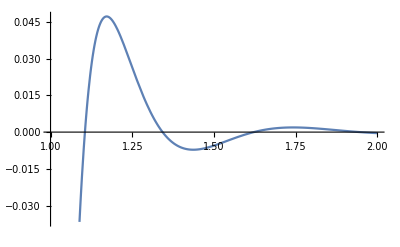

```mathematica
Plot[CompoundMatrixMethod[{λ,λ0},sys/.ϵ->0.1],{λ0,1,2}]
```

FindRoot will converge to different roots for different starting points:

```mathematica
FindRoot[CompoundMatrixMethod[{λ,λ0},sys/.ϵ->1/10],{λ0,1.1}]
FindRoot[CompoundMatrixMethod[{λ,λ0},sys/.ϵ->1/10],{λ0,1.3}]
FindRoot[CompoundMatrixMethod[{λ,λ0},sys/.ϵ->1/10],{λ0,1.6}]
FindRoot[CompoundMatrixMethod[{λ,λ0},sys/.ϵ->1/10],{λ0,2}]
```

{λ0→1.10517}

{λ0→1.34269}

{λ0→1.62184}

{λ0→1.94586}

The plot of the function is continuous, but there is a sharp turning point around λ=1:

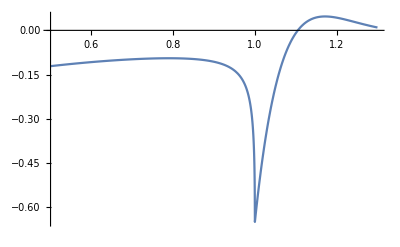

```mathematica
Plot[CompoundMatrixMethod[{λ,λ0},sys/.ϵ->0.1],{λ0,0.5,1.3},PlotRange->All]
```

Zooming in:

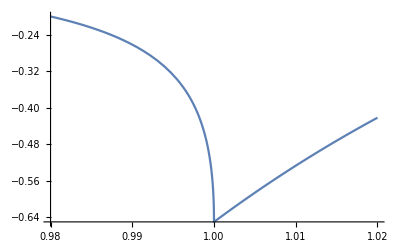

```mathematica
Plot[CompoundMatrixMethod[{λ,λ0},sys/.ϵ->0.1],{λ0,0.98,1.02},PlotRange->All]
```

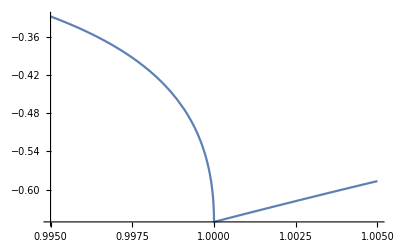

```mathematica
Plot[CompoundMatrixMethod[{λ,λ0},sys/.ϵ->0.1],{λ0,0.995,1.005},PlotRange->All]
```

This occurs when the eigenvalues of the matrix A at x=π/2 become entirely imaginary. In general this happens when eigenvalues at either endpoint change type. However, the function is still continuous here.

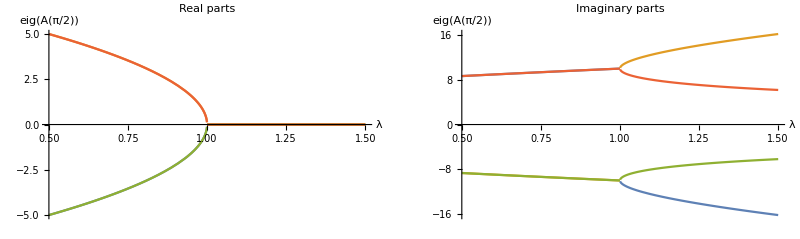

```mathematica
GraphicsRow[{Plot[Evaluate[Re@Eigenvalues[sys[[1]]/.ϵ->1/10/.x->π/2]],{λ,0.5,1.5},PlotLabel->"Real parts", AxesLabel->{"λ","eig(A(π/2))"}],Plot[Evaluate[Im@Eigenvalues[sys[[1]]/.ϵ->1/10/.x->π/2]],{λ,0.5,1.5},PlotLabel->"Imaginary parts",AxesLabel->{"λ","eig(A(π/2))"}]},ImageSize->800]
```

Example 5: Tenth order equation with constant coefficients

An example of a 10x10 matrix equation, subject to symmetric boundary conditions at x=0,1.

```mathematica
A2={{0,1,0,0,0,0,5,0,-5,0},{0,0,1,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0},{-625 ω,-125/2,2,0,0,3,-300,0,300,0},{0,0,0,0,0,1,0,0,0,0},{0,0,0,-1.5,0.5,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,0},{0,-169,0,0,0,0,9175+694 ω,0,811,0},{0,0,0,0,0,0,0,0,0,1},{0,672,0,0,0,0,3222,0,-709+694 ω,0}};
```

Takes a few seconds  for the first evaluation while it builds up the 10 x10 matrix, faster  for the subsequent ones.

```mathematica
CompoundMatrixMethod[{ω,1},A2,DiagonalMatrix[{0,1,1,0,1,0,0,1,0,1}],DiagonalMatrix[{0,1,1,0,1,0,0,1,0,1}],{x,0,1}]//AbsoluteTiming
```

{0.593231,-0.672945}

Each point takes longer to evaluate to evaluate for a large system like this, so ListPlot works better than Plot.

```mathematica
CompoundMatrixMethod[{ω,1},A2,DiagonalMatrix[{0,1,1,0,1,0,0,1,0,1}],DiagonalMatrix[{0,1,1,0,1,0,0,1,0,1}],{x,0,1}]//AbsoluteTiming
```

{0.648369,-0.672945}

We can see there are a number of positive eigenvalues:

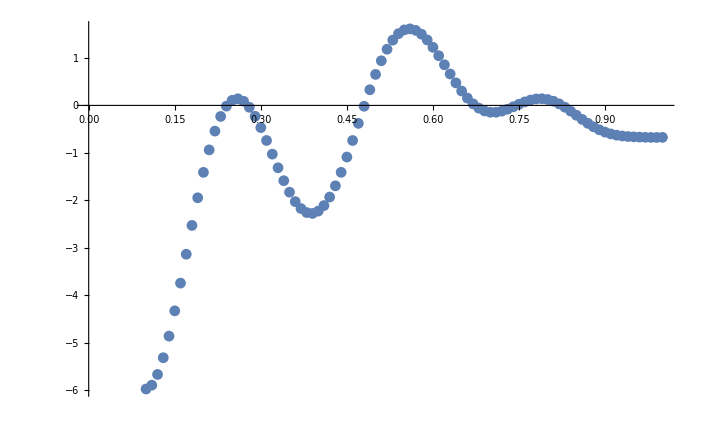

```mathematica
ListPlot[Table[{ωω,CompoundMatrixMethod[{ω,ωω},A2,DiagonalMatrix[{0,1,1,0,1,0,0,1,0,1}],DiagonalMatrix[{0,1,1,0,1,0,0,1,0,1}],{x,0,1}]},{ωω,0.1,1,0.01}]]
```

```mathematica
FindRoot[CompoundMatrixMethod[{ω,ωω},A2,DiagonalMatrix[{0,1,1,0,1,0,0,1,0,1}],DiagonalMatrix[{0,1,1,0,1,0,0,1,0,1}],{x,0,1}],{ωω,0.2}]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{ωω→0.24095}

```mathematica
FindRoot[CompoundMatrixMethod[{ω,ωω},A2,DiagonalMatrix[{0,1,1,0,1,0,0,1,0,1}],DiagonalMatrix[{0,1,1,0,1,0,0,1,0,1}],{x,0,1}],{ωω,0.3}]
```

{ωω→0.277395}

```mathematica
FindRoot[CompoundMatrixMethod[{ω,ωω},A2,DiagonalMatrix[{0,1,1,0,1,0,0,1,0,1}],DiagonalMatrix[{0,1,1,0,1,0,0,1,0,1}],{x,0,1}],{ωω,0.5}]
```

{ωω→0.480499}

```mathematica
FindRoot[CompoundMatrixMethod[{ω,ωω},A2,DiagonalMatrix[{0,1,1,0,1,0,0,1,0,1}],DiagonalMatrix[{0,1,1,0,1,0,0,1,0,1}],{x,0,1}],{ωω,0.7}]
```

{ωω→0.673238}

```mathematica
FindRoot[CompoundMatrixMethod[{ω,ωω},A2,DiagonalMatrix[{0,1,1,0,1,0,0,1,0,1}],DiagonalMatrix[{0,1,1,0,1,0,0,1,0,1}],{x,0,1}],{ωω,0.72}]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{ωω→0.745249}

```mathematica
FindRoot[CompoundMatrixMethod[{ω,ωω},A2,DiagonalMatrix[{0,1,1,0,1,0,0,1,0,1}],DiagonalMatrix[{0,1,1,0,1,0,0,1,0,1}],{x,0,1}],{ωω,0.8}]
```

{ωω→0.824797}

Example 6: Fourth order equation with non-constant coefficients and infinite endpoints

An example with an infinite domain requiring the function w to decay at both ends. 
The equation is (d^4 w)/dx^4-(d^2 w)/dx^2+2(d^2(w w_0))/dx^2+λ w =0, where w_0(x)=3/2 sech^2(x/2), with w decaying at both positive and negative infinity. 
We can get the matrix by not giving boundary conditions in ToLinearMatrixForm:

```mathematica
(A4=(ToLinearMatrixForm[w''''[x]-w''[x]+2D[w0[x]w[x],{x,2}]+λ w[x]==0,{},w,{x,-L,L}]/.w0->Function[{x},3/2 Sech[x/2]^2])[[1]])//MatrixForm
```

(0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1
-λ-2 (-3/4 Sech[x/2]^4+3/2 Sech[x/2]^2 Tanh[x/2]^2) | 6 Sech[x/2]^2 Tanh[x/2] | 1-3 Sech[x/2]^2 | 0)

To ensure that the function to decay at both ends, we find the eigenvectors of the limiting matrix A as x approaches infinity. At negative (positive) infinity, the function must approach those eigenvectors corresponding to  positive (negative) eigenvalues of the function at these ends.

Two functions, SelectPositiveEigenvectors (SelectNegativeEigenvectors) are used to extract the eigenvectors corresponding to positive (negative) eigenvalues at negative (positive) infinity. This requires the eigenvalue to be substituted into the matrix to work.

```mathematica
SelectNegativeEigenvectors[A4/.λ->1,x]//N//Chop//MatrixForm
```

(0.-1. ⅈ | 0.5+0.866025 ⅈ | -0.866025-0.5 ⅈ | 1.
0.+1. ⅈ | 0.5-0.866025 ⅈ | -0.866025+0.5 ⅈ | 1.)

However, the CompoundMatrixMethod function will do this automatically if not given boundary conditions:

```mathematica
sys=ToLinearMatrixForm[w''''[x]-w''[x]+2D[w0[x]w[x],{x,2}]+λ w[x]==0,{},w,{x,-L,L}]/.w0->Function[{x},3/2 Sech[x/2]^2];
```

So we can set up a function that evaluates for a given λ_0 and domain length L_0:

```mathematica
example4a[λ0_?NumericQ,L0_?NumericQ]:=CompoundMatrixMethod[{λ,λ0},sys/.L->L0]
```

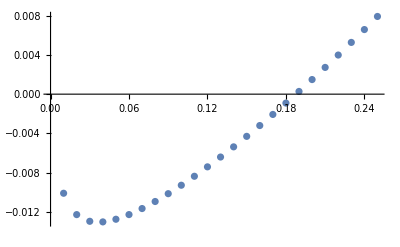

```mathematica
ListPlot[Table[{λ0,example4a[λ0,10]},{λ0,0.01,0.25,0.01}]]
```

Varying the position at which the end point “infinity” conditions are applied at converges to the root (λ_0=3/8):

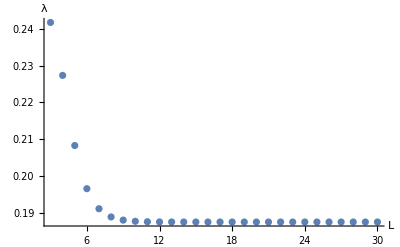

```mathematica
rootposa=Table[{L,λ0}/.FindRoot[example4a[λ0,L],{λ0,0.2}],{L,3,30}]//Quiet;
ListPlot[rootposa,PlotRange->All,AxesLabel->{"L","λ"}]
```

Alternatively, we can solve the same equation but use the fact it is an even function to split at zero (so w'(0)=w'''(0)=0).

```mathematica
sys2=ToLinearMatrixForm[w''''[x]-w''[x]+2D[w0[x]w[x],{x,2}]+λ w[x]==0,{w'[0]==0,w'''[0]==0},w,{x,0,L}]/.w0->Function[{x},3/2 Sech[x/2]^2];
```

```mathematica
example4b[λ0_?NumericQ,L0_?NumericQ]:=CompoundMatrixMethod[{λ,λ0},sys2/.L->L0]
```

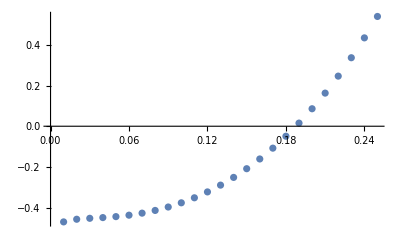

```mathematica
ListPlot[Table[{λ0,example4b[λ0,10]},{λ0,0.01,0.25,0.01}]]
```

Position of the roots are identical for the two methods of solution:

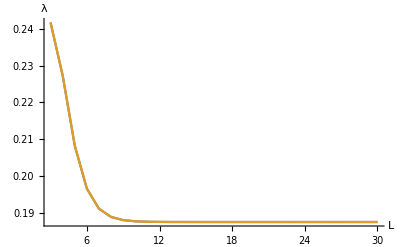

```mathematica
rootposb=Table[{L,λ0}/.FindRoot[example4b[λ0,L],{λ0,0.2}],{L,3,30}];
ListLinePlot[{rootposa,rootposb},PlotRange->All,AxesLabel->{"L","λ"}]
```

Even if the two functions give different outputs, their roots are in the same place (note the scale change required for the second one).

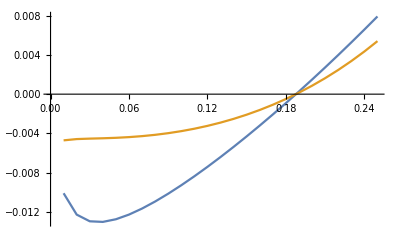

```mathematica
ListLinePlot[{Table[{λ0,example4a[λ0,10]},{λ0,0.01,0.25,0.01}],Table[{λ0,example4b[λ0,10]/100},{λ0,0.01,0.25,0.01}]},Joined->True]
```

Example 7: Sixth order system, constructing neutral curves as parameters vary

Linear stability equations for cylinder rotating inside another, [ϵ^2 ∂_yy - 1]^2u(y) = ϵ^2 T V(y) v(y),  [ϵ^2 ∂_yy -1] v(y) = ϵ^2 T u(y) V' (y), ϵ u'(y) + I w(y) =0, where V(y) = 1-y.

Set up the equations, note that the equation for w does not contain any derivatives, but the code handles that appropriately.

```mathematica
dd=(ϵ^2 D[#,{y,2}]-#)&;
{dd[dd[u[y]]]==ϵ^2 T V[y]v[y],dd[v[y]]==ϵ^2 u[y]V'[y],ϵ u'[y]+ I w[y]==0}
```

{u[y]-ϵ^2 u''[y]+ϵ^2 (-u''[y]+ϵ^2 u^(4)[y])==T ϵ^2 v[y] V[y],-v[y]+ϵ^2 v''[y]==ϵ^2 u[y] V'[y],ⅈ w[y]+ϵ u'[y]==0}

```mathematica
sys=ToLinearMatrixForm[{dd[dd[u[y]]]==ϵ^2 T V[y]v[y],dd[v[y]]==ϵ^2 u[y]V'[y],ϵ u'[y]+ I w[y]==0},{u[0]==0,v[0]==0,w[0]==0,u[1]==0,v[1]==0,w[1]==0},{u,v,w},{y,0,1}]
```

{{{0,1,0,0,0,0},{0,0,1,0,0,0},{0,0,0,1,0,0},{-1/ϵ^4,0,2/ϵ^2,0,(T V[y])/ϵ^2,0},{0,0,0,0,0,1},{V'[y],0,0,0,1/ϵ^2,0}},{{1,0,0,0,0,0},{0,0,0,0,1,0},{0,ⅈ ϵ,0,0,0,0}},{{1,0,0,0,0,0},{0,0,0,0,1,0},{0,ⅈ ϵ,0,0,0,0}},{y,0,1}}

Define a function to calculate the Evans function for a given ϵ and T:

```mathematica
Clear[tempfn];
tempfn[ee_?NumericQ,T0_?NumericQ]:=CompoundMatrixMethod[{T,T0},sys/.V->Function[{y},1-y]/.ϵ->ee]
```

Find a value of T for ϵ = 0.1:

```mathematica
CompoundMatrixMethod[{T,1},(sys/.V->Function[{y},1-y]/.ϵ->0.1)]
```

3.1251×10^-7

```mathematica
FindRoot[tempfn[1/10,t],{t,20000}]
```

{t→26242.5}

Loop through varying ϵ to construct sections of a neutral curve. Start at the previous value to stay along the same curve (takes a while to follow the roots)

```mathematica
lastroot={T0->26242};
etab=Monitor[Table[lastroot=FindRoot[tempfn[e,T0],{T0,T0/.lastroot},DampingFactor->0.2];{e,T0}/.lastroot,{e,0.1,1,0.1}],e];//Quiet
```

```mathematica
lastroot={T0->26242};
etab2=Monitor[Table[lastroot=FindRoot[tempfn[e,T0],{T0,1.4*T0/.lastroot},DampingFactor->0.2];{e,T0}/.lastroot,{e,Reverse@Range[0.03,0.1,0.005]}],e];//Quiet
```

Plot the neutral curve:

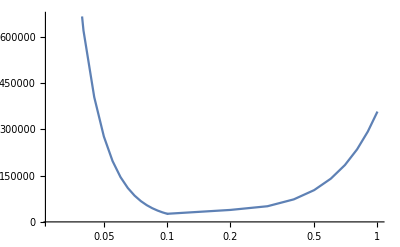

```mathematica
ListLogLinearPlot[Sort@(Join@@{etab,etab2}),Joined->True]
```

There is another neutral curve at higher values of T:

```mathematica
lastroot={T0->226242};
etab3=Monitor[Table[lastroot=FindRoot[tempfn[e,T0],{T0,T0/.lastroot},DampingFactor->0.2];{e,T0}/.lastroot,{e,0.1,1,0.1}],e];
```

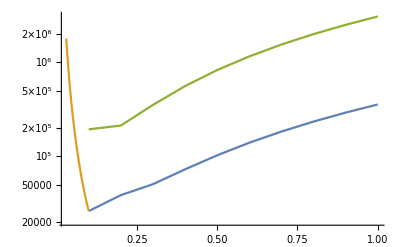

```mathematica
ListLogPlot[{etab,etab2,etab3},Joined->True,PlotRange->All]
```

These additional roots for a given value of T can seen when plotting at a fixed value of ϵ:

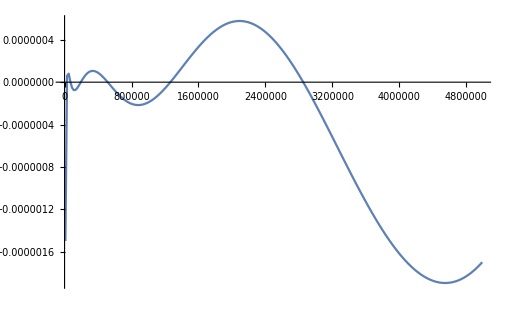

```mathematica
Table[{tt,tempfn[0.1,tt]},{tt,10^4,5*10^6,2*10^4}]//ListLinePlot
```

Example 8: Fourth order system with an interface, constant coefficients

The method also works for interface problems, where different equations are being solved in two domains with some kind of matching conditions in the middle.

Set up some arbitrary equations to be solved in the two regimes, for eigenvalue σ,
y''''(x)+5 y''(x)+σ^4 y(x)==0       in x_1≤x≤x_2
z''''(x)-σ^4 z(x)==0                               in x_2≤x≤x_3
subject to
y'(x_1)=0, y''(x_1)=0, z'(x_3)=0, z'''(x_3)=0
with interface conditions
y(x_2)=z(x_2),      y'(x_2)+y'''(x_2)=-2z'(x_2)+z(x_2)-z'''(x_2),    3 y''(x_2)=0.2 z(x_2)+2z''(x_2)-5z'''(x_2),   -3 y'''(x_2)=z'(x_2)-z'''(x_2)

```mathematica
x1=-5;x2=1;x3=2;
eq1=y''''[x]+5 y''[x]+σ^4 y[x]==0;
eq2=z''''[x]-σ^4 z[x]==0;
matchconds={y[x2]==z[x2],y'[x2]+y'''[x2]==-2z'[x2]+z[x2]-z'''[x2],3y''[x2]==0.2z[x2]+2z''[x2]-5z'''[x2],-3y'''[x2]==z'[x2]-z'''[x2]};
bcs1={y'[x1]==0,y''[x1]==0};
bcs2={z'[x3]==0,z'''[x3]==0};
```

These equations are simple enough to be solved exactly in the two regions:

```mathematica
ysub=DSolve[eq1,y,x][[1]]
zsub=DSolve[eq2,z,x,GeneratedParameters->(C[#+4]&)][[1]]
```

{y→Function[{x},ⅇ^((x √(-5-√(25-4 σ^4)))/(√2)) C[1]+ⅇ^(-(x √(-5-√(25-4 σ^4)))/(√2)) C[2]+ⅇ^((x √(-5+√(25-4 σ^4)))/(√2)) C[3]+ⅇ^(-(x √(-5+√(25-4 σ^4)))/(√2)) C[4]]}

{z→Function[{x},ⅇ^(-x σ) C[6]+ⅇ^(x σ) C[8]+C[5] Cos[x σ]+C[7] Sin[x σ]]}

Substituting these solutions into the boundary and matching conditions, we can find a coefficient matrix for the constants C[i]:

```mathematica
(coefmat=Transpose[Table[Coefficient[Join[bcs1,bcs2,matchconds]/.ysub/.zsub/.Equal->Subtract,ii],{ii,Array[C,4+4]}]])//MatrixForm
```

((ⅇ^(-(5 √(-5-√(25-4 σ^4)))/(√2)) √(-5-√(25-4 σ^4)))/(√2) | -(ⅇ^((5 √(-5-√(25-4 σ^4)))/(√2)) √(-5-√(25-4 σ^4)))/(√2) | (ⅇ^(-(5 √(-5+√(25-4 σ^4)))/(√2)) √(-5+√(25-4 σ^4)))/(√2) | -(ⅇ^((5 √(-5+√(25-4 σ^4)))/(√2)) √(-5+√(25-4 σ^4)))/(√2) | 0 | 0 | 0 | 0
1/2 ⅇ^(-(5 √(-5-√(25-4 σ^4)))/(√2)) (-5-√(25-4 σ^4)) | 1/2 ⅇ^((5 √(-5-√(25-4 σ^4)))/(√2)) (-5-√(25-4 σ^4)) | 1/2 ⅇ^(-(5 √(-5+√(25-4 σ^4)))/(√2)) (-5+√(25-4 σ^4)) | 1/2 ⅇ^((5 √(-5+√(25-4 σ^4)))/(√2)) (-5+√(25-4 σ^4)) | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -σ Sin[2 σ] | -ⅇ^(-2 σ) σ | σ Cos[2 σ] | ⅇ^(2 σ) σ
0 | 0 | 0 | 0 | σ^3 Sin[2 σ] | -ⅇ^(-2 σ) σ^3 | -σ^3 Cos[2 σ] | ⅇ^(2 σ) σ^3
ⅇ^((√(-5-√(25-4 σ^4)))/(√2)) | ⅇ^(-(√(-5-√(25-4 σ^4)))/(√2)) | ⅇ^((√(-5+√(25-4 σ^4)))/(√2)) | ⅇ^(-(√(-5+√(25-4 σ^4)))/(√2)) | -Cos[σ] | -ⅇ^-σ | -Sin[σ] | -ⅇ^σ
(ⅇ^((√(-5-√(25-4 σ^4)))/(√2)) √(-5-√(25-4 σ^4)))/(√2)+(ⅇ^((√(-5-√(25-4 σ^4)))/(√2)) (-5-√(25-4 σ^4))^(3/2))/(2 √2) | -(ⅇ^(-(√(-5-√(25-4 σ^4)))/(√2)) √(-5-√(25-4 σ^4)))/(√2)-(ⅇ^(-(√(-5-√(25-4 σ^4)))/(√2)) (-5-√(25-4 σ^4))^(3/2))/(2 √2) | (ⅇ^((√(-5+√(25-4 σ^4)))/(√2)) √(-5+√(25-4 σ^4)))/(√2)+(ⅇ^((√(-5+√(25-4 σ^4)))/(√2)) (-5+√(25-4 σ^4))^(3/2))/(2 √2) | -(ⅇ^(-(√(-5+√(25-4 σ^4)))/(√2)) √(-5+√(25-4 σ^4)))/(√2)-(ⅇ^(-(√(-5+√(25-4 σ^4)))/(√2)) (-5+√(25-4 σ^4))^(3/2))/(2 √2) | -Cos[σ]-2 σ Sin[σ]+σ^3 Sin[σ] | -ⅇ^-σ-2 ⅇ^-σ σ-ⅇ^-σ σ^3 | 2 σ Cos[σ]-σ^3 Cos[σ]-Sin[σ] | -ⅇ^σ+2 ⅇ^σ σ+ⅇ^σ σ^3
-15/2 ⅇ^((√(-5-√(25-4 σ^4)))/(√2))-3/2 ⅇ^((√(-5-√(25-4 σ^4)))/(√2)) √(25-4 σ^4) | -15/2 ⅇ^(-(√(-5-√(25-4 σ^4)))/(√2))-3/2 ⅇ^(-(√(-5-√(25-4 σ^4)))/(√2)) √(25-4 σ^4) | -15/2 ⅇ^((√(-5+√(25-4 σ^4)))/(√2))+3/2 ⅇ^((√(-5+√(25-4 σ^4)))/(√2)) √(25-4 σ^4) | -15/2 ⅇ^(-(√(-5+√(25-4 σ^4)))/(√2))+3/2 ⅇ^(-(√(-5+√(25-4 σ^4)))/(√2)) √(25-4 σ^4) | -0.2 Cos[σ]+2 σ^2 Cos[σ]+5 σ^3 Sin[σ] | -0.2 ⅇ^-σ-2 ⅇ^-σ σ^2-5 ⅇ^-σ σ^3 | -5 σ^3 Cos[σ]-0.2 Sin[σ]+2 σ^2 Sin[σ] | -0.2 ⅇ^σ-2 ⅇ^σ σ^2+5 ⅇ^σ σ^3
(15 ⅇ^((√(-5-√(25-4 σ^4)))/(√2)) √(-5-√(25-4 σ^4)))/(2 √2)+(3 ⅇ^((√(-5-√(25-4 σ^4)))/(√2)) √(25-4 σ^4) √(-5-√(25-4 σ^4)))/(2 √2) | -(15 ⅇ^(-(√(-5-√(25-4 σ^4)))/(√2)) √(-5-√(25-4 σ^4)))/(2 √2)-(3 ⅇ^(-(√(-5-√(25-4 σ^4)))/(√2)) √(25-4 σ^4) √(-5-√(25-4 σ^4)))/(2 √2) | (15 ⅇ^((√(-5+√(25-4 σ^4)))/(√2)) √(-5+√(25-4 σ^4)))/(2 √2)-(3 ⅇ^((√(-5+√(25-4 σ^4)))/(√2)) √(25-4 σ^4) √(-5+√(25-4 σ^4)))/(2 √2) | -(15 ⅇ^(-(√(-5+√(25-4 σ^4)))/(√2)) √(-5+√(25-4 σ^4)))/(2 √2)+(3 ⅇ^(-(√(-5+√(25-4 σ^4)))/(√2)) √(25-4 σ^4) √(-5+√(25-4 σ^4)))/(2 √2) | σ Sin[σ]+σ^3 Sin[σ] | ⅇ^-σ σ-ⅇ^-σ σ^3 | -σ Cos[σ]-σ^3 Cos[σ] | -ⅇ^σ σ+ⅇ^σ σ^3)

We can find zeroes of the determinant of this matrix using FindRoot:

```mathematica
detRoots={σ,0}/.(FindRoot[Det[coefmat],{σ,#}]&/@{1.3,1.5,2,4})//Chop//Quiet;
```

This determinant method struggles for more complicated systems.
Instead we can use the function ToLinearMatrixForm to convert this system into the appropriate form for the compound matrix method:

```mathematica
sys4=ToLinearMatrixForm[{eq1,eq2},{bcs1,bcs2,matchconds},{y,z},{x,x1,x2,x3}]
```

{{{{0,1,0,0},{0,0,1,0},{0,0,0,1},{-σ^4,0,-5,0}},{{0,1,0,0},{0,0,1,0},{0,0,0,1},{σ^4,0,0,0}}},{{0,1,0,0},{0,0,1,0}},{{0,1,0,0},{0,0,0,1}},{{{1,0,0,0},{0,1,0,1},{0,0,3,0},{0,0,0,-3}},{{-1,0,0,0},{-1,2,0,1},{-0.2,0,-2,5},{0,-1,0,1}}},{x,-5,1,2}}

Now given a test value of σ, we can find the Evans function there:

```mathematica
CompoundMatrixMethod[{σ,1},sys4]
```

-11.0729

And then plot the Evans function as we change the value of σ, and we find the same values as the determinant method:

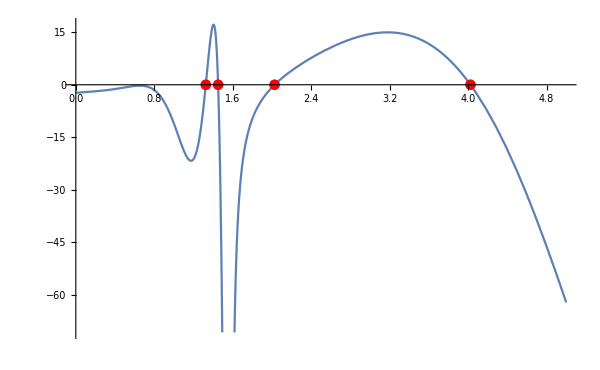

```mathematica
Show[Plot[CompoundMatrixMethod[{σ,ss},sys4],{ss,0,5}],ListPlot[detRoots,PlotStyle->Red],ImageSize->600]
```

Example 9 : Second order system with interface

Define the equations and endpoints:

```mathematica
x1=-2;x2=0;x3=5;
eq1=y''[x]-2y'[x]+σ^2 y[x]==0;
eq2=z''[x]-(5+1/5)z'[x]-σ^2 z[x]==0;
matchconds={y[x2]==z[x2],y'[x2]+y[x2]==-2z'[x2]+z[x2]};
bcs1={y'[x1]==0};
bcs2={z[x3]==0};
```

We can solve this explicitly:

```mathematica
ysub=DSolve[eq1,y,x][[1]];
zsub=DSolve[eq2,z,x,GeneratedParameters->(C[#+2]&)][[1]];
det=Transpose[Table[Coefficient[Join[bcs1,bcs2,matchconds]/.ysub/.zsub/.Equal->Subtract,ii],{ii,Array[C,4]}]]//Det//Simplify;
```

NSolve is not very good at finding roots for this system, and that the symbolic solution includes spurious solutions at values where the ODE has a repeated root, e.g. σ= ±1, ±2.6 ⅈ.

```mathematica
nsol=NSolve[{det==0,0.1<Abs[σ]<10},σ]
```

{{σ→-5.85664+0. ⅈ},{σ→-1.+0. ⅈ},{σ→0.-2.6 ⅈ},{σ→0.+2.6 ⅈ},{σ→0.-2.68176 ⅈ},{σ→0.+2.68176 ⅈ},{σ→0.-2.91216 ⅈ},{σ→0.+2.91216 ⅈ},{σ→0.-3.25753 ⅈ},{σ→0.+3.25753 ⅈ},{σ→1.+0. ⅈ},{σ→5.85664+0. ⅈ}}

FindRoot is better:

```mathematica
roots=Table[FindRoot[det2==0,{σ,ii}],{ii,{1.6,3,4.4}}]//Quiet//Chop
```

{{σ→1.61479},{σ→2.88141},{σ→4.33898}}

Set up the system and plot it:

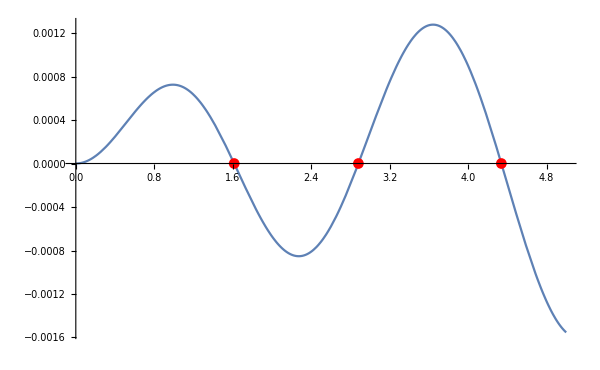

```mathematica
syss=ToLinearMatrixForm[{eq1,eq2},{bcs1,bcs2,matchconds},{y,z},{x,x1,x2,x3}];
Show[Plot[CompoundMatrixMethod[{σ,ss},syss],{ss,0,5}],ListPlot[{σ,0}/.roots,PlotStyle->Red],ImageSize->600]
```

Example 10: Fourth order, eigenvalue in the integration range

In this example, the ‘eigenvalue’ is the length of the domain, and also appears in the equation.

```mathematica
ode=w''''[x]+(L-x) w''[x]-w'[x]== 0;
BCs={w[0]==0,w'[0]==0,w''[L]== 0,w'''[L]==0};
```

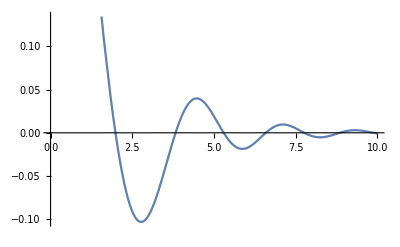

```mathematica
sys=ToLinearMatrixForm[ode,BCs,w,{x,0,L}];
Plot[CompoundMatrixMethod[{L,L0},sys],{L0,0,10}]
```

```mathematica
FindRoot[CompoundMatrixMethod[{L,L0},sys],{L0,2.5}]
```

{L0→1.98635}